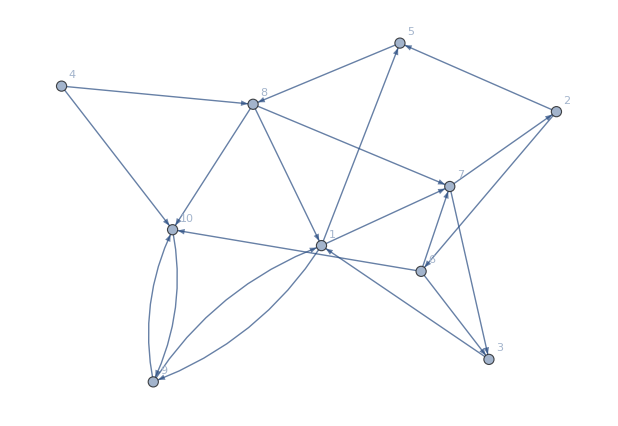

```mathematica
randomGraph=RandomGraph[{10,20},DirectedEdges->True,VertexLabels->Automatic]
```

```mathematica
VertexList[randomGraph,x_/;OddQ@VertexDegree[randomGraph,x]]
```

{2,3,5,7,8,10}

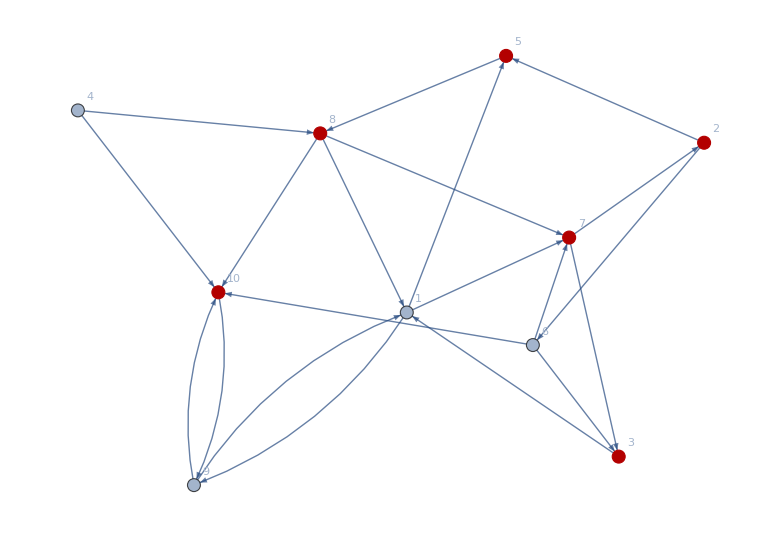

```mathematica
HighlightGraph[randomGraph,VertexList[randomGraph,x_/;OddQ@VertexDegree[randomGraph,x]]]
```

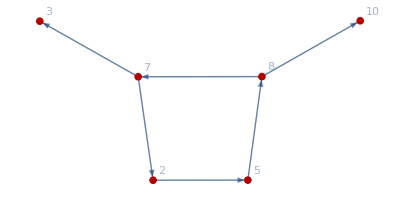

```mathematica
Subgraph[HighlightGraph[randomGraph,VertexList[randomGraph,x_/;OddQ@VertexDegree[randomGraph,x]]],VertexList[randomGraph,x_/;OddQ@VertexDegree[randomGraph,x]]]
```

```mathematica
FindEdgeCover[Subgraph[HighlightGraph[randomGraph,VertexList[randomGraph,x_/;OddQ@VertexDegree[randomGraph,x]]],VertexList[randomGraph,x_/;OddQ@VertexDegree[randomGraph,x]]]]
```

{2->5,7->3,8->10}

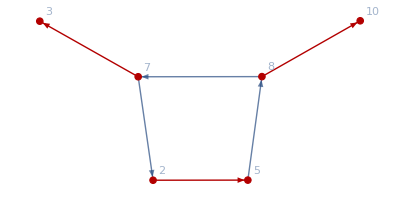

```mathematica
HighlightGraph[Graph[{2,3,5,7,8,10},{SparseArray[Automatic,{6,6},0,{1,{{0,1,1,2,4,6,6},{{3},{5},{1},{2},{4},{6}}},Pattern}],Null},{VertexLabels->{Automatic},GraphHighlight->{10,5,2,7,8,3}}],{2->5,7->3,8->10}]
```

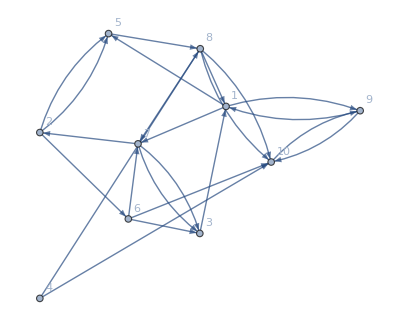

```mathematica
EdgeAdd[randomGraph,FindEdgeCover[Subgraph[HighlightGraph[randomGraph,VertexList[randomGraph,x_/;OddQ@VertexDegree[randomGraph,x]]],VertexList[randomGraph,x_/;OddQ@VertexDegree[randomGraph,x]]]]]
```

```mathematica
EulerianGraphQ[EdgeAdd[randomGraph,FindEdgeCover[Subgraph[HighlightGraph[randomGraph,VertexList[randomGraph,x_/;OddQ@VertexDegree[randomGraph,x]]],VertexList[randomGraph,x_/;OddQ@VertexDegree[randomGraph,x]]]]]]
```

False